# Notebook associated to Finding bifurcations in mathematical epidemiology via reaction network methods [1]

by N. Vassena, F. Avram, and R. Adenane

ABSTRACT (original article): 
 CITATION (original article):

## Constants definition and numerical conditions

Defining constants directly to speed up computation of numerical model.

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];

Format[γr]:=Subscript[γ,r];Format[γs]:=Subscript[γ,s]; Format[γi]:=Subscript[γ,i];
Format[μr]:=Subscript[μ,r];Format[μs]:=Subscript[μ,s];Format[μi]:=Subscript[μ,i]; 

sd= (λ (γr+μr))/(γs μr+γr μs+μr μs); R0= (sd β)/(a+γi+μi)  ; rd= Λ/μ- sd;
b0= ((a+γi+μi) (γs μr+γr μs+μr μs))/(λ (γr+μr)); 

cncut={λ->1+11 ξ/10,a->(ξ-3)^2,b->ξ-4,γr->1,μr->1,μs->1/10,μi->2,β->1,γi->1,γs->1}(*Numerical condition with ξ kept unknown*);

csi={s->ξ,i->1}(*semi-numerical endemic point*);

(*critical value of ξH when Hopf bifurcation arise*)
xiH=1/620 *(4351-√584161);
```

We define the symbolic model using a stoichiometric matrix S and a vector of rates Vg, then we specialize the model in the case of non linear treatment function and linear incidence function:

```mathematica
var= { s, i, r};
S={{1,-1,0,1,-1,-1,0,0},
   {0,1,-1,0,0,0,-1,0},
   {0,0,1,-1,1,0,0,-1}};(*The stochiometric matrix*)
Vg={λ, f[s,i],h[i], γr r, γs s,s μs,i μi ,r  μr};
RHS=S . Vg;   
par = Complement[Variables[RHS], var]; 
Print["The symbolic  RHS ",RHS//MatrixForm , " has ", par//Length , " par given by ",par]

(*The case of quadratic f(s,i) and Michaelis Menten h(i)*)
cex={f[s,i]->β s i, h[i]->γi i+ a i/(1+b i)};
RHSx= RHS//.cex; parx=Complement[Variables[RHSx], var]; cpx=Thread[parx>0];
RHSxn=RHSx//.cncut

Print["When f is quadratic  and h is Michaelis Menten, the  RHS becomes ", RHSx//MatrixForm ,
" and it has ", parx//Length, " pars",parx ]

Print["check total= ",Total[RHSx]//FullSimplify]
```

The symbolic  RHS (r γ_r-s γ_s+λ-s μ_s-f[s,i]
-i μ_i+f[s,i]-h[i]
-r γ_r+s γ_s-r μ_r+h[i]) has 8 par given by {γ_r,γ_s,λ,μ_i,μ_r,μ_s,f[s,i],h[i]}

{1+r-(11 s)/10-i s+(11 ξ)/10,-3 i+i s-(i (-3+ξ)^2)/(1+i (-4+ξ)),i-2 r+s+(i (-3+ξ)^2)/(1+i (-4+ξ))}

When f is quadratic  and h is Michaelis Menten, the  RHS becomes (-i s β+r γ_r-s γ_s+λ-s μ_s
-(a i)/(1+b i)+i s β-i γ_i-i μ_i
(a i)/(1+b i)+i γ_i-r γ_r+s γ_s-r μ_r) and it has 10 pars{a,b,β,γ_i,γ_r,γ_s,λ,μ_i,μ_r,μ_s}

check total= λ-i μ_i-r μ_r-s μ_s

## Time and parametric plots suggest the existence of periodic solutions at different values of ξ

IIlustration of the time and phase plot when ξ=6 (when the eigenvalues
of the Jacobian at the unstable endemic point are (−2.33284, 0.116421 ± 1.23678 Im)) , suggest the existence of a stable limit cycle:

{{s→InterpolatingFunction[…],i→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

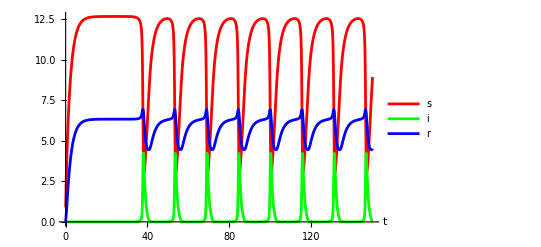

plT6.pdf

```mathematica
Xt=Map[#[t]&,var ];
ct=Thread[var->Xt];
RHSt=RHSxn/.ct;
ss=RHSt[[1]] ;
ii=RHSt[[2]];
rr=RHSt[[3]]; 
T=150; c6={ξ->6};
T1=50;
X0={0.9,0.05,0.05};
ode={s'[t]==ss,i'[t]==ii,r'[t]==rr,s[0]==X0[[1]],i[0]==X0[[2]],r[0]==X0[[3]]};
odeN=ode/.c6;
sol=NDSolve[odeN,var,{t,0,T}]

plT=Plot[Evaluate@{  s[t]/.sol,i[t]/.sol,r[t]/.sol},{t,0,T},PlotRange->Full,
PlotStyle->{Red,Green,Blue},AxesLabel->{"t",""},PlotLegends->{"s","i","r"}]

pp=ParametricPlot[{  s[t],i[t]}/.sol,{t,0,T1}, AxesLabel->{"s","i"},PlotStyle->{Red},Epilog->
{{PointSize[Large],Point[{X0[[1]],X0[[2]]}]},Text["(s_0,i_0)",Offset[{10,8},{X0[[1]],X0[[2]]}]]},AxesOrigin->{0,0}];
Show[pp,PlotRange->All];
Export["plT6.pdf",plT]
```

We produce now   parametric plots when  ξ=6 suggesting convergence to a limit cycle around the endemic point,  both when starting from inside and outside the cycle. Note the apparent intersection between the paths is due to the fact that we are projecting three dimensional paths in two dimensions.

The unstable endemic point has the following coordinates

{6.,1.}

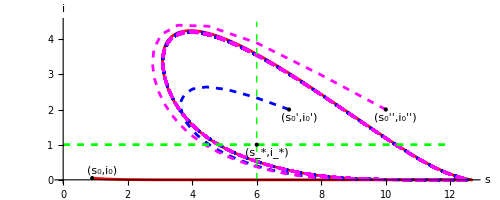

ppF.pdf

```mathematica
(*Now by strating from inside the cycle*)
X02={7,2,1.5}(*Different initial values*);
ode={s'[t]==ss,i'[t]==ii,r'[t]==rr,s[0]==X02[[1]],i[0]==X02[[2]],r[0]==X02[[3]]};
T=300;
odeN=ode/.c6;
sol=NDSolve[odeN,var,{t,0,T}];

pp1=ParametricPlot[{  s[t],i[t]}/.sol,{t,0,T}, AxesLabel->{"s","i"},
PlotRange->Full,PlotStyle->{Dashed,Blue}];

(*Now by strating again from outside the cycle*)
X03={10,2,1.5}(*Different initial values*);
ode={s'[t]==ss,i'[t]==ii,r'[t]==rr,s[0]==X03[[1]],i[0]==X03[[2]],r[0]==X03[[3]]};
T=300;
odeN=ode/.c6;
sol=NDSolve[odeN,var,{t,0,T}];

pp2=ParametricPlot[{  s[t],i[t]}/.sol,{t,0,T}, AxesLabel->{"s","i"},
PlotRange->Full,PlotStyle->{Dashed,Magenta}];

pyn=Plot[(1),{t,0,12},PlotStyle->{Dashed,Green}](*plot of the value of endemic i*);

 Print["The unstable endemic point has the following coordinates "]
   fp={ξ,1}//.c6//N
   
ppF=Show[{pp,pp1,pp2,Graphics[{Green,Dashed,
Line[{{fp[[1]],0},{fp[[1]],4.5}}]}],pyn},
Epilog->{Text["(s_0,i_0)",Offset[{10,8},{X0[[1]],X0[[2]]}]],
{PointSize[Large],Point[{X0[[1]],X0[[2]]}]},{Text["(s_*,i_*)",Offset[{10,-8},{(fp[[1]]),(fp[[2]])}]],
{PointSize[Large],Style[Point[{(fp[[1]]),(fp[[2]])}],Cyan]}},
{PointSize[Large],Point[{X02[[1]],X02[[2]]}]},
Text["(s_0',i_0')",Offset[{10,-8},{X02[[1]],X02[[2]]}]], {PointSize[Large],Point[{X03[[1]],X03[[2]]}]},
Text["(s_0'',i_0'')",Offset[{10,-8},{X03[[1]],X03[[2]]}]]},PlotRange->All]
Export["ppF.pdf",ppF]
```

IIlustration of the time plot when ξ=ξH ( the eigenvalues of the Jacobian at the endemic point are (−2.31501, ±1.29094 Im)) suggest the  existence of a unique limit cycle :

{{s→InterpolatingFunction[…],i→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

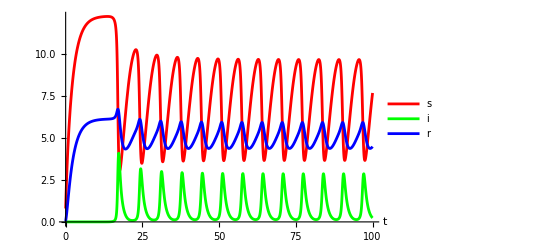

plTH.pdf

```mathematica
X0={0.8,0.05,0.05} (*Initial conditions*);
ode={s'[t]==ss,i'[t]==ii,r'[t]==rr,s[0]==X0[[1]],i[0]==X0[[2]],r[0]==X0[[3]]};
T=300;
odeN=ode/.ξ->xiH;
sol=NDSolve[odeN,var,{t,0,T}]

plT=Plot[Evaluate@{  s[t]/.sol,i[t]/.sol,r[t]/.sol},{t,0,T/3},PlotRange->Full,
PlotStyle->{Red,Green,Blue},AxesLabel->{"t",""},PlotLegends->{"s","i","r"}]

Export["plTH.pdf",plT]
```

In the following, we chose different starting points, and we illustrate the time plots of s from different initial points. This suggests again the existence of a unique limit cycle:

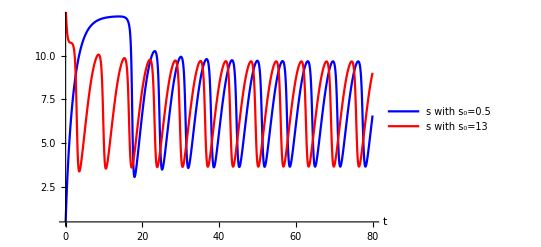

plTHs.pdf

```mathematica
X0={0.5,0.05,0.05} (*Initial conditions*);
ode={s'[t]==ss,i'[t]==ii,r'[t]==rr,s[0]==X0[[1]],i[0]==X0[[2]],r[0]==X0[[3]]};
T=300;
odeN=ode/.ξ->xiH;
sol=NDSolve[odeN,var,{t,0,T}];

plT1=Plot[Evaluate@{  s[t]/.sol},{t,0,80},PlotRange->Full,
PlotStyle->{Blue},AxesLabel->{"t",""},PlotLegends->{"s with s_0=0.5"}];

X0={13,0.02,0.01} (*Different Initial conditions*);
ode={s'[t]==ss,i'[t]==ii,r'[t]==rr,s[0]==X0[[1]],i[0]==X0[[2]],r[0]==X0[[3]]};
T=300;
odeN=ode/.ξ->xiH;
sol=NDSolve[odeN,var,{t,0,T}];

plT2=Plot[Evaluate@{  s[t]/.sol},{t,0,80},PlotRange->Full,
PlotStyle->{Red},AxesLabel->{"t",""},PlotLegends->{"s with s_0=13"}];


tot=Show[plT1,plT2]

Export["plTHs.pdf",tot]
```

## Analysis of the saddle node bifurcation dis=0:

In this cell we give an alternative solution to the zero eigenvalue bifurcation point, using also the script RUR in our package Epid, which reduces the fixed point system to a scalar polynomial. This allows also a quick computation of a Bogdanov-Takens point.

```mathematica
<<Epid.wl;
mod={RHSx,var,parx};
pol=(RUR[mod,2][[2]]/i//Simplify)[[1]];
dis=Discriminant[pol,i];
cof=CoefficientList[dis,β]//FullSimplify;
Print["discriminant of RUR pol is a polyn of degree ",cof//Length-1," in β, with disc",dib=Discriminant[dis,β]//FullSimplify,
" which is always positive"]
so=Solve[dis==0,β]//FullSimplify;
Print["There are two critical β"]
Timing[ze=Solve[Append[cpx,dis==0],β]//FullSimplify]
Print["which may both be positive",so//.Append[Drop[cncut,{8}],ξ->xiH]//N]
jacx=Grad[RHSx,var]//.{s->ξ,i->1,r->ξ-1};jacx//MatrixForm
tra2=Tr[jacx];
cncutt=Drop[cncut,{-3}];
eq=Flatten[Append[cpx,dis==0&&tra2==0]];
BTP=Solve[eq//.cncutt,{β,ξ}]//Flatten;
Print["On the cut, there is a unique BTP  with dis= tr=0: ",BTP," = ",BTP//N ]
```

discriminant of RUR pol is a polyn of degree (-1+Length)[{b^2 (γ_i+μ_i)^2 (γ_s μ_r+(γ_r+μ_r) μ_s)^2,-2 b (γ_r μ_i (2 a+γ_i+μ_i)+(γ_i+μ_i) (a+γ_i+μ_i) μ_r+b λ (γ_i+μ_i) (γ_r+μ_r)) (γ_s μ_r+(γ_r+μ_r) μ_s),b^2 λ^2 (γ_r+μ_r)^2+2 b λ (γ_r+μ_r) (γ_r μ_i+(-a+γ_i+μ_i) μ_r)+(γ_r μ_i+(a+γ_i+μ_i) μ_r)^2}] in β, with disc16 a b^2 (γ_r μ_i+(γ_i+μ_i) μ_r) (γ_r μ_i (a+γ_i+μ_i)+b λ (γ_i+μ_i) (γ_r+μ_r)) (γ_s μ_r+(γ_r+μ_r) μ_s)^2 which is always positive

There are two critical β

{0.125,{{β→ConditionalExpression[(b (γ_s μ_r+(γ_r+μ_r) μ_s) (γ_r μ_i (2 a+γ_i+μ_i)+(γ_i+μ_i) (a+γ_i+μ_i) μ_r+b λ (γ_i+μ_i) (γ_r+μ_r)-2 √(a (γ_r μ_i+(γ_i+μ_i) μ_r) (γ_r μ_i (a+γ_i+μ_i)+b λ (γ_i+μ_i) (γ_r+μ_r))) Sign[b^2 λ^2 (γ_r+μ_r)^2+2 b λ (γ_r+μ_r) (γ_r μ_i+(-a+γ_i+μ_i) μ_r)+(γ_r μ_i+(a+γ_i+μ_i) μ_r)^2]))/(b^2 λ^2 (γ_r+μ_r)^2+2 b λ (γ_r+μ_r) (γ_r μ_i+(-a+γ_i+μ_i) μ_r)+(γ_r μ_i+(a+γ_i+μ_i) μ_r)^2), a>0&&b>0&&γ_i>0&&γ_r>0&&γ_s>0&&λ>0&&μ_i>0&&μ_r>0&&μ_s>0]},{β→ConditionalExpression[(b (γ_s μ_r+(γ_r+μ_r) μ_s) (γ_r μ_i (2 a+γ_i+μ_i)+(γ_i+μ_i) (a+γ_i+μ_i) μ_r+b λ (γ_i+μ_i) (γ_r+μ_r)+2 √(a (γ_r μ_i+(γ_i+μ_i) μ_r) (γ_r μ_i (a+γ_i+μ_i)+b λ (γ_i+μ_i) (γ_r+μ_r))) Sign[b^2 λ^2 (γ_r+μ_r)^2+2 b λ (γ_r+μ_r) (γ_r μ_i+(-a+γ_i+μ_i) μ_r)+(γ_r μ_i+(a+γ_i+μ_i) μ_r)^2]))/(b^2 λ^2 (γ_r+μ_r)^2+2 b λ (γ_r+μ_r) (γ_r μ_i+(-a+γ_i+μ_i) μ_r)+(γ_r μ_i+(a+γ_i+μ_i) μ_r)^2), a>0&&b>0&&γ_i>0&&γ_r>0&&γ_s>0&&λ>0&&μ_i>0&&μ_r>0&&μ_s>0]}}}

which may both be positive{{β→0.0706311},{β→0.82476}}

(-β-γ_s-μ_s | -β ξ | γ_r
β | (a b)/(1+b)^2-a/(1+b)-γ_i-μ_i+β ξ | 0
γ_s | -(a b)/(1+b)^2+a/(1+b)+γ_i | -γ_r-μ_r)

On the cut, there is a unique BTP  with dis= tr=0: {β→Root0.993Root[-153533737+208688880 #1-42449100 #1^2-16544000 #1^3+4470000 #1^4&,2]0.9931659750483545,ξ→324385/30457-(4244910 Root0.993Root[-153533737+208688880 #1-42449100 #1^2-16544000 #1^3+4470000 #1^4&,2]0.9931659750483545)/2162447-(1654400 (Root0.993Root[-153533737+208688880 #1-42449100 #1^2-16544000 #1^3+4470000 #1^4&,2]0.9931659750483545)^2)/2162447+(447000 (Root0.993Root[-153533737+208688880 #1-42449100 #1^2-16544000 #1^3+4470000 #1^4&,2]0.9931659750483545)^3)/2162447} = {β→0.993166,ξ→8.14886}

Reference: [1] Finding bifurcations in mathematical epidemiology via reaction network methods , by N. Vassena, F. Avram, and R. Adenane. Submitted to Chaos - an interdisciplinary journal of nonlinear science

## CITE THIS NOTEBOOK